## ConnectionList-example.nb ConnectionMatrix / ConnectionList example

Example Cellzilla2D notebook.

GPL License applies. 
See http://xlr8r.info and http://cellzilla.info for further details.

```mathematica
<<xlr8r.m
```

xCellerator 0.95 (28-Feb-2014) loaded Tue 6 Jun 2017 17:24:34
using Mathematica 11.1.1 for Mac OS X x86 (64-bit) (April 27, 2017) (Version 11.1, Release 1)

```mathematica
<<Cellzilla2D.m
```

Cellzilla2D (3.0.51 (05 June 2017)) loaded Tue 6 Jun 2017 17:24:37
using xCellerator 0.95 and XSSA ** Not Found **
GPL License Terms Apply

Warning: Cellzilla2D: xSSA.m not found in path. Some stochastic conversion functions may not work as expected. It should be loaded manually before any xSSA (stochastic) simulations can be run.

Generate  random vertices to use as Voronoi Centers

```mathematica
r:=RandomReal[{0,100}]; 
vertices=Table[{r,r}, {10}];
```

Use the Voronoi Centers to generate a tissue with 5 cells using the Bounded-Cell-Voronoi algorithm

```mathematica
w=BoundedCellVoronoi[vertices];
```

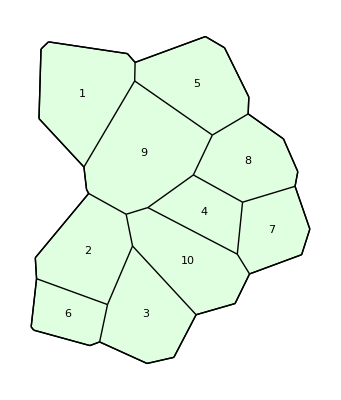

```mathematica
ShowTissue[w, "CellNumbers"-> True]
```

Determine the Connection List

```mathematica
ConnectionList[w]
```

{{1,5},{1,9},{2,3},{2,6},{2,9},{2,10},{3,2},{3,6},{3,10},{4,7},{4,8},{4,9},{4,10},{5,1},{5,8},{5,9},{6,2},{6,3},{7,4},{7,8},{7,10},{8,4},{8,5},{8,7},{8,9},{9,1},{9,2},{9,4},{9,5},{9,8},{9,10},{10,2},{10,3},{10,4},{10,7},{10,9}}

```mathematica
ConnectionList[w, "UpperTriangular"-> True]
```

{{1,5},{1,9},{2,3},{2,6},{2,9},{2,10},{3,6},{3,10},{4,7},{4,8},{4,9},{4,10},{5,8},{5,9},{7,8},{7,10},{8,9},{9,10}}

Now find the connection matrix.

```mathematica
ConnectionMatrix[w]
```

SparseArray[<36>, {10, 10}]

```mathematica
MatrixForm[ConnectionMatrix[w]]
```

(0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 1 | 0
0 | 0 | 1 | 0 | 0 | 1 | 0 | 0 | 1 | 1
0 | 1 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 0 | 1 | 1 | 1 | 1
1 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 1 | 0
0 | 1 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 1 | 0 | 1
0 | 0 | 0 | 1 | 1 | 0 | 1 | 0 | 1 | 0
1 | 1 | 0 | 1 | 1 | 0 | 0 | 1 | 0 | 1
0 | 1 | 1 | 1 | 0 | 0 | 1 | 0 | 1 | 0)

```mathematica
MatrixForm[ConnectionMatrix[w, "UpperTriangular"-> True]]
```

(0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 1 | 0
0 | 0 | 1 | 0 | 0 | 1 | 0 | 0 | 1 | 1
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 0 | 1 | 1 | 1 | 1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1)